# BDF Font translation

### Initialization

```mathematica
Off[General::spell,General::spell1]
```

### Function to expand hex numbers into bits

```mathematica
HexExpand=Function[{hex},Sign[BitAnd[ToExpression["16^^"<>hex],#]]&/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]
```

Function[{hex},(Sign[BitAnd[ToExpression[16^^<>hex],#1]]&)/@Table[2^b,{b,4 StringLength[hex]-1,0,-1}]]

### Function to compress bit array into words

```mathematica
WordBuild=Function[{bitarray},Fold[2#1+#2&,0,bitarray]]
```

Function[{bitarray},Fold[2 #1+#2&,0,bitarray]]

## Import and process

```mathematica
SetDirectory["../src"]
```

/home/cmaier/Hackerspaces/sinobit/zpix-pixel-font/src

```mathematica
FileNames[]
```

{Zpix.bdf,Zpix.vfb}

```mathematica
bdflines=StringSplit/@Import["Zpix.bdf","Lines"];
```

```mathematica
Take[bdflines,200]
```

{{STARTFONT,2.1},{FONT,-FontForge-Zpix-Normal-R-Normal--12-120-75-75-P-119-ISO10646-1},{SIZE,12,75,75},{FONTBOUNDINGBOX,19,13,-5,-2},{COMMENT,"Generated,by,fontforge,,http://fontforge.sourceforge.net"},{STARTPROPERTIES,39},{FOUNDRY,"FontForge"},{FAMILY_NAME,"Zpix"},{WEIGHT_NAME,"Normal"},{SLANT,"R"},{SETWIDTH_NAME,"Normal"},{ADD_STYLE_NAME,""},{PIXEL_SIZE,12},{POINT_SIZE,120},{RESOLUTION_X,75},{RESOLUTION_Y,75},{SPACING,"P"},{AVERAGE_WIDTH,119},{CHARSET_REGISTRY,"ISO10646"},{CHARSET_ENCODING,"1"},{FONTNAME_REGISTRY,""},{CHARSET_COLLECTIONS,"ASCII,ISOLatin1Encoding,ISO8859-5,JISX0208.1997,GB2312.1980,BIG5,ISO10646-1"},{FONT_NAME,"Zpix"},{FACE_NAME,"ZpixEX2"},{FONT_VERSION,"2.0"},{FONT_ASCENT,10},{FONT_DESCENT,2},{UNDERLINE_POSITION,-1},{UNDERLINE_THICKNESS,1},{X_HEIGHT,6},{CAP_HEIGHT,8},{RAW_ASCENT,796},{RAW_DESCENT,203},{NORM_SPACE,5},{RELATIVE_WEIGHT,40},{RELATIVE_SETWIDTH,50},{SUPERSCRIPT_X,0},{SUPERSCRIPT_Y,6},{SUPERSCRIPT_SIZE,6},{SUBSCRIPT_X,0},{SUBSCRIPT_Y,0},{SUBSCRIPT_SIZE,6},{FIGURE_WIDTH,6},{AVG_LOWERCASE_WIDTH,89},{AVG_UPPERCASE_WIDTH,95},{ENDPROPERTIES},{CHARS,22043},{STARTCHAR,space},{ENCODING,32},{SWIDTH,333,0},{DWIDTH,4,0},{BBX,1,1,13,-2},{BITMAP},{00},{ENDCHAR},{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,300,0},{DWIDTH,6,0},{BBX,1,9,2,0},{BITMAP},{80},{80},{80},{80},{80},{80},{00},{80},{80},{ENDCHAR},{STARTCHAR,quotedbl},{ENCODING,34},{SWIDTH,378,0},{DWIDTH,6,0},{BBX,3,2,1,7},{BITMAP},{A0},{A0},{ENDCHAR},{STARTCHAR,numbersign},{ENCODING,35},{SWIDTH,601,0},{DWIDTH,6,0},{BBX,5,9,0,0},{BITMAP},{50},{50},{F8},{50},{50},{50},{F8},{50},{50},{ENDCHAR},{STARTCHAR,dollar},{ENCODING,36},{SWIDTH,628,0},{DWIDTH,6,0},{BBX,5,11,0,-1},{BITMAP},{20},{70},{A8},{A0},{60},{20},{30},{28},{A8},{70},{20},{ENDCHAR},{STARTCHAR,percent},{ENCODING,37},{SWIDTH,968,0},{DWIDTH,6,0},{BBX,6,8,0,0},{BITMAP},{48},{A8},{B0},{50},{28},{34},{54},{48},{ENDCHAR},{STARTCHAR,ampersand},{ENCODING,38},{SWIDTH,769,0},{DWIDTH,6,0},{BBX,5,9,0,0},{BITMAP},{60},{90},{90},{60},{40},{A8},{A8},{90},{68},{ENDCHAR},{STARTCHAR,quotesingle},{ENCODING,39},{SWIDTH,203,0},{DWIDTH,6,0},{BBX,1,2,2,7},{BITMAP},{80},{80},{ENDCHAR},{STARTCHAR,parenleft},{ENCODING,40},{SWIDTH,359,0},{DWIDTH,6,0},{BBX,3,11,2,-1},{BITMAP},{20},{40},{40},{80},{80},{80},{80},{80},{40},{40},{20},{ENDCHAR},{STARTCHAR,parenright},{ENCODING,41},{SWIDTH,359,0},{DWIDTH,6,0},{BBX,3,11,1,-1},{BITMAP},{80},{40},{40},{20},{20},{20},{20},{20},{40},{40},{80},{ENDCHAR},{STARTCHAR,asterisk},{ENCODING,42},{SWIDTH,437,0},{DWIDTH,6,0},{BBX,5,5,0,2},{BITMAP},{20},{20},{F8},{20}}

```mathematica
Transpose[Flatten[Position[bdflines,#]]&/@{{"STARTCHAR",_},{"ENDCHAR"}}];
Dimensions[charlines=Take[bdflines,#]&/@%]
```

{22043}

```mathematica
charlines⟦1⟧
```

{{STARTCHAR,space},{ENCODING,32},{SWIDTH,333,0},{DWIDTH,4,0},{BBX,1,1,13,-2},{BITMAP},{00},{ENDCHAR}}

```mathematica
charlines⟦2⟧
```

{{STARTCHAR,exclam},{ENCODING,33},{SWIDTH,300,0},{DWIDTH,6,0},{BBX,1,9,2,0},{BITMAP},{80},{80},{80},{80},{80},{80},{00},{80},{80},{ENDCHAR}}

```mathematica
Dimensions[charcodes=Last[Flatten[Select[#,First[#]=="ENCODING"&]]]&/@charlines]
```

{22043}

```mathematica
Dimensions[widths=Flatten[Select[#,First[#]=="DWIDTH"&]]⟦2⟧&/@charlines]
```

{22043}

```mathematica
Dimensions[boundingboxes=Flatten[Select[#,First[#]=="BBX"&]]&/@charlines]
```

{22043,5}

```mathematica
Dimensions[sizes=Take[#,{2,3}]&/@ToExpression[boundingboxes]]
```

{22043,2}

```mathematica
maxsize=MapThread[Apply,{{Max,Max},Transpose[sizes]}]
```

{12,12}

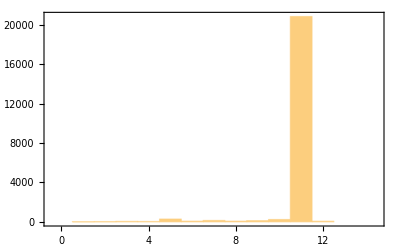

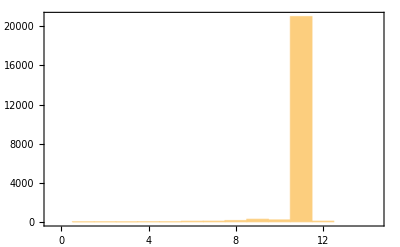

```mathematica
Print[Histogram[#,{-1/2,29/2,1},Frame->True,PlotRange->All]]&/@Transpose[sizes];
```

1
25 | 2
36 | 3
56 | 4
45 | 5
294 | 6
79 | 7
150 | 8
79 | 9
127 | 10
247 | 11
20832 | 12
73
1
27 | 2
28 | 3
23 | 4
35 | 5
31 | 6
76 | 7
84 | 8
147 | 9
281 | 10
212 | 11
21015 | 12
84

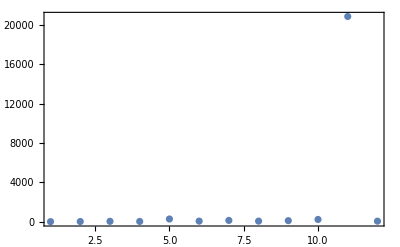

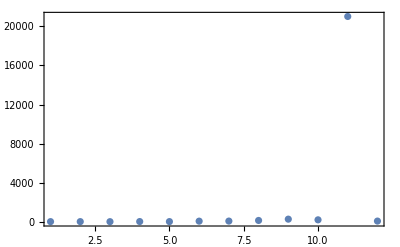

```mathematica
TableForm[Sort[Tally[#],#1⟦1⟧<#2⟦1⟧&]&/@Transpose[sizes]]
Print[ListPlot[#,Frame->True,PlotRange->All]]&/@%;
```

```mathematica
bounds=Flatten[{Take[#,-2],Take[#,-2]+Take[#,{2,3}]}]&/@ToExpression[boundingboxes];
```

```mathematica
bigbox=MapThread[Apply,{{Min,Min,Max,Max},Transpose[bounds]}]
```

{-5,-2,14,11}

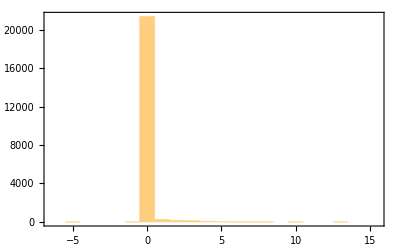

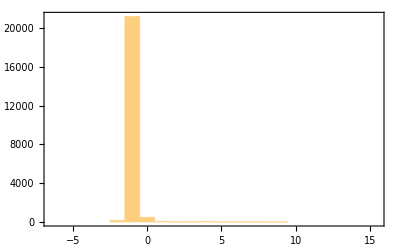

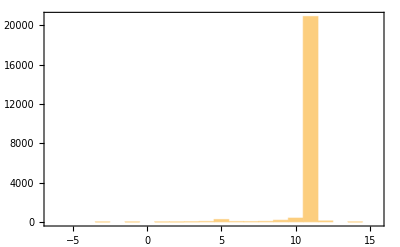

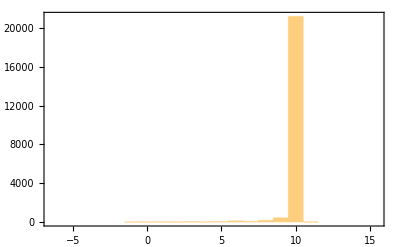

```mathematica
Print[Histogram[#,{-13/2,31/2,1},Frame->True,PlotRange->All]]&/@Transpose[bounds];
```

-5
2 | -1
1 | 0
21400 | 1
246 | 2
155 | 3
128 | 4
55 | 5
35 | 6
9 | 7
8 | 8
2 | 10
1 | 13
1 |  | 
-2
149 | -1
21225 | 0
475 | 1
54 | 2
20 | 3
26 | 4
47 | 5
6 | 6
15 | 7
13 | 8
10 | 9
3 |  |  | 
-3
1 | -1
1 | 1
3 | 2
4 | 3
24 | 4
50 | 5
247 | 6
43 | 7
38 | 8
56 | 9
174 | 10
395 | 11
20903 | 12
103 | 14
1
-1
3 | 0
3 | 1
7 | 2
4 | 3
13 | 4
5 | 5
41 | 6
102 | 7
56 | 8
155 | 9
419 | 10
21232 | 11
3 |  |

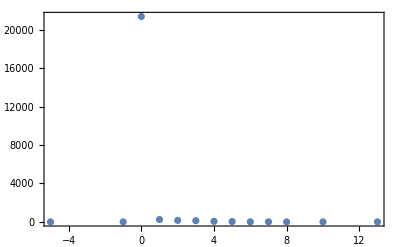

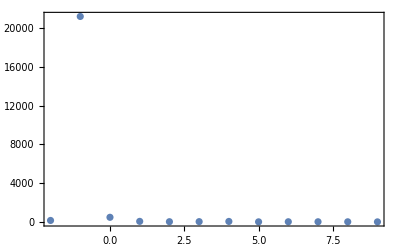

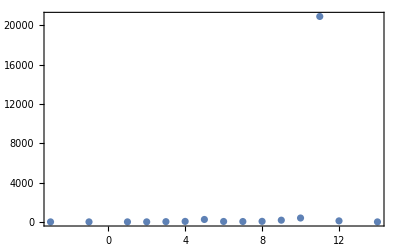

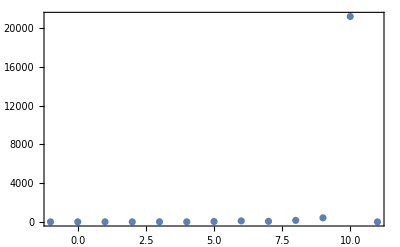

```mathematica
TableForm[Sort[Tally[#],#1⟦1⟧<#2⟦1⟧&]&/@Transpose[bounds]]
Print[ListPlot[#,Frame->True,PlotRange->All]]&/@%;
```

```mathematica
fills=#-bigbox&/@bounds;
```

```mathematica
Take[fills,128]
```

{{18,0,0,-12},{7,2,-11,-2},{6,9,-10,-2},{5,2,-9,-2},{5,1,-9,-1},{5,2,-8,-3},{5,2,-9,-2},{7,9,-11,-2},{7,1,-9,-1},{6,1,-10,-1},{5,4,-9,-4},{5,4,-9,-4},{5,0,-12,-10},{5,6,-9,-6},{7,2,-11,-9},{6,2,-10,-2},{5,2,-9,-2},{6,2,-11,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{7,3,-11,-3},{5,2,-12,-3},{5,2,-9,-2},{5,4,-9,-5},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,1,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{5,2,-9,-2},{7,1,-10,-1},{6,2,-10,-2},{7,1,-10,-1},{5,9,-10,-2},{5,0,-8,-12},{5,9,-12,-2},{5,2,-9,-4},{5,2,-9,-2},{5,2,-9,-4},{5,2,-9,-2},{5,2,-9,-4},{5,2,-10,-2},{5,1,-9,-4},{5,2,-9,-2},{6,2,-10,-2},{5,1,-11,-2},{5,2,-9,-2},{6,2,-10,-2},{5,2,-9,-4},{5,2,-9,-4},{5,2,-9,-4},{5,1,-9,-4},{5,1,-9,-4},{6,2,-9,-4},{5,2,-9,-4},{5,2,-10,-2},{5,2,-9,-4},{5,2,-9,-4},{5,2,-9,-4},{5,2,-9,-4},{5,1,-9,-4},{5,2,-9,-4},{7,1,-9,-1},{8,0,-10,-1},{6,1,-10,-1},{5,9,-8,-1},{7,1,-11,-2},{5,1,-9,-3},{5,2,-9,-1},{6,2,-4,-2},{5,2,-9,-2},{7,0,-11,-1},{8,1,-6,-1},{7,7,-6,-4},{5,2,-9,-3},{5,6,-9,-2},{5,3,-9,-3},{5,5,-9,-5},{6,6,-9,-6},{5,2,-9,-3},{6,10,-9,-2},{5,9,-11,-1},{7,2,-5,-2},{5,6,-10,-2},{5,6,-10,-2},{7,10,-10,-1},{9,0,-5,-5},{5,1,-8,-1},{9,5,-7,-5},{7,1,-10,-9},{6,6,-11,-2},{5,6,-10,-2},{5,3,-9,-3},{5,2,-9,-1},{5,2,-9,-1},{5,2,-9,-1},{5,2,-10,-2},{5,2,-9,-1},{5,2,-9,-1}}

```mathematica
Dimensions[bounds]
```

{22043,4}

```mathematica
Dimensions[bitmaps=Function[{line},
Block[{bounds=ToExpression[Drop[Flatten[Select[line,First[#]=="BBX"&]],1]]},
1-Take[HexExpand[#],bounds⟦1⟧]&/@Flatten[Take[line,{1,-1}+Flatten[Position[line,#]&/@{{"BITMAP"},{"ENDCHAR"}}]]]
]
]/@charlines]
```

{22043}

```mathematica
Take[bitmaps,16]
```

{{{1}},{{0},{0},{0},{0},{0},{0},{1},{0},{0}},{{0,1,0},{0,1,0}},{{1,0,1,0,1},{1,0,1,0,1},{0,0,0,0,0},{1,0,1,0,1},{1,0,1,0,1},{1,0,1,0,1},{0,0,0,0,0},{1,0,1,0,1},{1,0,1,0,1}},{{1,1,0,1,1},{1,0,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{1,0,0,1,1},{1,1,0,1,1},{1,1,0,0,1},{1,1,0,1,0},{0,1,0,1,0},{1,0,0,0,1},{1,1,0,1,1}},{{1,0,1,1,0,1},{0,1,0,1,0,1},{0,1,0,0,1,1},{1,0,1,0,1,1},{1,1,0,1,0,1},{1,1,0,0,1,0},{1,0,1,0,1,0},{1,0,1,1,0,1}},{{1,0,0,1,1},{0,1,1,0,1},{0,1,1,0,1},{1,0,0,1,1},{1,0,1,1,1},{0,1,0,1,0},{0,1,0,1,0},{0,1,1,0,1},{1,0,0,1,0}},{{0},{0}},{{1,1,0},{1,0,1},{1,0,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{0,1,1},{1,0,1},{1,0,1},{1,1,0}},{{0,1,1},{1,0,1},{1,0,1},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,1,0},{1,0,1},{1,0,1},{0,1,1}},{{1,1,0,1,1},{1,1,0,1,1},{0,0,0,0,0},{1,1,0,1,1},{1,0,1,0,1}},{{1,1,0,1,1},{1,1,0,1,1},{0,0,0,0,0},{1,1,0,1,1},{1,1,0,1,1}},{{1,0},{1,0},{0,1}},{{0,0,0,0,0}},{{0},{0}},{{1,1,0},{1,1,0},{1,1,0},{1,0,1},{1,0,1},{1,0,1},{0,1,1},{0,1,1},{0,1,1}}}

```mathematica
BitmapExtend=Function[{bitmap,fill},
Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},
bmp=Join[xl,#,xr]&/@bitmap;
yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];
yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];
Join[yt,bmp,yb]
]
]
```

Function[{bitmap,fill},Block[{bmp,xl=Table[1,{☺,fill⟦1⟧}],xr=Table[1,{☺,-fill⟦3⟧}],yt,yb},bmp=(Join[xl,#1,xr]&)/@bitmap;yb=Table[Table[1,{☺,Length[First[bmp]]}],{☹,fill⟦2⟧}];yt=Table[Table[1,{☺,Length[First[bmp]]}],{☹,-fill⟦4⟧}];Join[yt,bmp,yb]]]

```mathematica
Dimensions[extbitmaps=MapThread[BitmapExtend,{bitmaps,fills}]]
```

{22043,13,19}

```mathematica
bitmapgrafix=MapThread[Graphics[Raster[Reverse[#1]],Frame->True,AspectRatio->Divide@@Dimensions[#1],FrameTicks->({#,#,{},{}}&[Range[0,16,4]]),PlotLabel->("code: 0x"<>IntegerString[ToExpression[#2],16,4])]&,{extbitmaps,charcodes}];
```

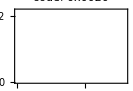

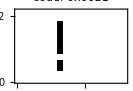

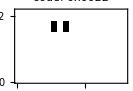

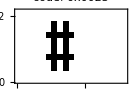

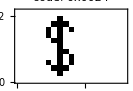

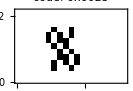

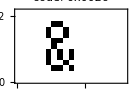

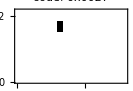

-Graphics-

-Graphics-

-Graphics-

«1929 more identical outputs»

```mathematica
Print/@Take[bitmapgrafix,{1,2048}];
```